## image5.nb

## Evolution of indirect reciprocity by image scoring NATURE |VOL 393 | 11 JUNE 1998

#### Martin A. Nowak*† & Karl Sigmund‡ * Department of Zoology, University of Oxford, Oxford OX1 3 PS, UK ‡ Institut fu.a8r Mathematik, Universita.a8t Wien, Strudlhofgasse 4, A - 1090 Wien, Austria

Assumptions
1. Random pairs of players are chosen, of which one is the potential donor of some altruistic act and the other is the recipient. The donor can cooperate and help the recipient at a cost c to himself, in which case the recipient receives a benefit of value b (with b > c).If the donor decides not to help, both individuals receive zero pay - off.（ペアがランダムに選ばれ，ドナーかレシピエント（受け手）の役割を与えられる．ドナーはコストcを払ってレシピエントに協力することができ，その場合レシピエントは利得bをもらえる．もしドナーが協力しない場合は双方利得0である）
   
2. Each player has an image score, s, which is known to every other player. If a player is chosen as a donor and decides to cooperate, then his (or her) image score increases by one unit; if the donor does not cooperate then it decreases by one unit.The image score of a recipient does not change.（各プレイヤーはイメージスコアsを持ち，ドナーになった際，協力すると+1，非協力すると-1変化する．レシピエントはsの値が変化しない）
   
3. We consider strategies where donors decide to help according to the image score of the recipient.A strategy is given by a number k : a player with this strategy provides help if, and only if, the image score of the potential recipient is at least k. The strategies are given by ki and the image levels by si. A donor, i, cooperates with a recipient, j, if ki <= sj. At the beginning of each generation, the image levels of all players are zero.The image scores range from-5 to +5, the strategy (k) values from -5 to +6. The strategy k =-5 represents unconditional cooperators, whereas the strategy k=6 represents defectors.（ドナーは協力するかどうかを自分の戦略kの値に応じて決定する．ドナーは自分の戦略kとレシピエントのイメージスコアsを比較して，k<=sの場合に協力する．各世代の最初はイメージスコアsは全て0である．sのレンジは[-5,5], kのレンジは[-5,6]である．k=-5は無条件協力者でk=6は常に非協力を意味する）
   
4. In succession, m donor - recipient pairs are chosen. The fitness of a player is given by the total number of points received during the m interactions.Some players may never be chosen, in which case their payoff from the game will be zero. On average, a player will be chosen 2 m/n times, either as donor or as recipient.（繰り返しにおいて，m個のドナー・レシピエントのペアが選択される．m回の相互行為の間に獲得した総利得に応じて，プレイヤーの適合度が決まる．）
   
5. At the end of each generation, players leave offspring in proportion to their fitness.（各世代の終わりに，プレイヤーは適合度に応じて子孫を残す）

## 概要：

### プログラムの流れ

```mathematica
0.初期値設定（集団人数n，戦略k，イメージスコアs等の初期値を決める）
1.マッチング
2.戦略決定（協力するか否かを決定する）
3.戦略に応じて得点を与える
4.イメージスコア（評判）を更新する
5.利得に応じて戦略kを切り替える

6.繰り返し
```

### 変数名一覧

```mathematica
n(*集団人数*)
id(*各個体の番号*)
klist(*戦略kのリスト*)
slist(*イメージスコアのリスト　*)
m(*マッチングするペアの数*)
benefit(*利得のリスト*)
generation(*繰り返し回数*)
kdist(* 戦略kの分布*)
```

### Moduleの定義

```mathematica
(* 戦略毎に適合度を決めた場合．
klist=RandomChoice[benefit->klist,n] を使った場合  *)
image12[n_(*人数*),m_(*ペアの数*),generations_(*繰り返し数*)]:=Module[{id,klist,slist,benefit,pair,kdist},
id=Range[n];
slist=Table[0,{n}];(* image score list *)
klist=Table[Random[Integer,{-5,6}],{n}];(* strategy list *)
benefit=Table[0,{n}];(*benefit list,  以上初期化 *)

Do[slist=Table[0,{n}];benefit=Table[0,{n}];(* 反復する際，イメージと利得は毎回初期化される *)
Do[(* 「pairを一個だけ作る操作」をDoでm回反復させて
m個のペアを作る．slistの情報はループの度に更新される *)
pair=RandomSample[id,2];(*Print["pair  ",pair];*)

If[klist⟦pair⟦1⟧⟧<=slist⟦pair⟦2⟧⟧,(* 協力条件 *)
(*協力時の処理*)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+1;
benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧-0.1;
slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧+1,
(*非協力時の処理*)
slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧-1];(* if 終わり*)
If[Min[benefit]<0,benefit=benefit+0.1,benefit=benefit](*　benefitの非負化，利得に応じてklistを更新するため　*)
,{m}];(*1generation内部でのペア選択　Do終わり*)

kdist=Table[0,{12}];(* 戦略k毎の利得分布 *)
Table[
Table[If[klist⟦i⟧==a-7,kdist⟦a⟧=kdist⟦a⟧+benefit⟦i⟧,kdist⟦a⟧=kdist⟦a⟧],{a,1,12}],{i,1,n}]
(*戦略毎に利得分布を求める *)
Table[klist⟦i⟧=If[Total[kdist]==0,klist⟦i⟧,
RandomChoice[kdist->Range[-6,5]]],{i,1,n}](* 利得の高い高い戦略は子孫を残しやすい *)
(* klistの途中経過の出力;kdist=BinCounts[klist,{-5,7,1}];Print[klist];
Print[kdist]*),{generations}](* Do 終わり*);

kdist=BinCounts[klist,{-5,7,1}];
ListPlot[Transpose[{Range[-6,5],kdist}],PlotRange->{-1,n+1},Filling->Axis,PlotStyle->PointSize[Large]]
]
```

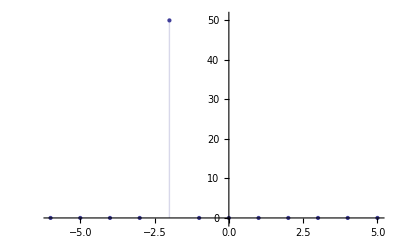

```mathematica
image12[50(*人数*),125(*ペアの数*),100(*繰り返し数*)]
```

## 練習問題

### ペアの数が協力者割合に及ぼす影響を分析しなさい

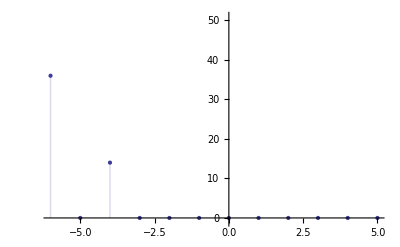

```mathematica
image12[50(*人数*),200(*ペアの数*),50(*繰り返し数*)]
```